# Hopf Bifurcation in Fast - Slow Van der Pol System

### Original Hopf Bifurcation, Unforced

Set Parameter Values

```mathematica
ϵ=.02;
```

Plot System Trajectories

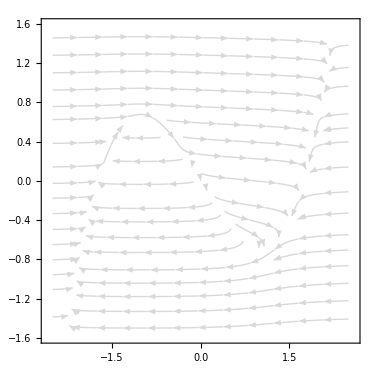

```mathematica
a=StreamPlot[{(x2 + (x1 - (x1^3)/3) ) /(ϵ),-x1-1.01},{x1,-2.5,2.5},{x2,-1.5,1.5},StreamStyle->LightGray]
```

Numerically solve system

```mathematica
f1[x1_,x2_,λ_]:=(x2 + (x1 - (x1^3)/3) ) /ϵ;
f2[x1_,x2_,λ_]:=-x1-.99746106843243;
```

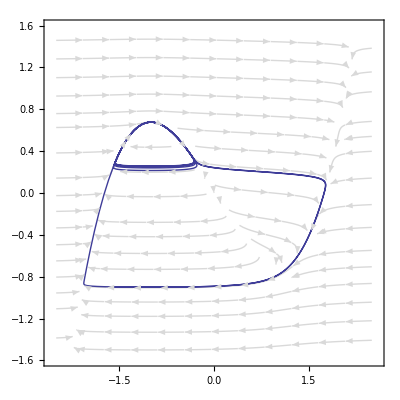

```mathematica
solution1 =NDSolve[{
x1'[t]==f1[x1[t],x2[t],0],
x2'[t]==f2[x1[t],x2[t],0],
x1[0]==-1.01,
x2[0]==.666},{x1,x2},{t,0,100},MaxSteps->2000001,MaxStepSize->.00005];
f=ParametricPlot[Evaluate[{x1[t],x2[t]}/.solution1],{t,80,100},PlotRange->{{-2.5,2.5},{-1.5,1.5}},PlotPoints->100];
Show[a,f]
```

### With Forcing

```mathematica
ff1[x1_,x2_,λ_]:=(x2 +λ + (x1 - (x1^3)/3) ) /ϵ;
ff2[x1_,x2_,λ_]:=-x1-1.01;
ffλ[t_]:= w r(2Pi) Sin[w t(2Pi)];
```

Reset parameter values

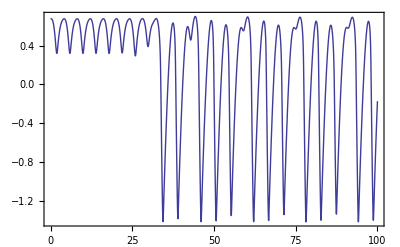

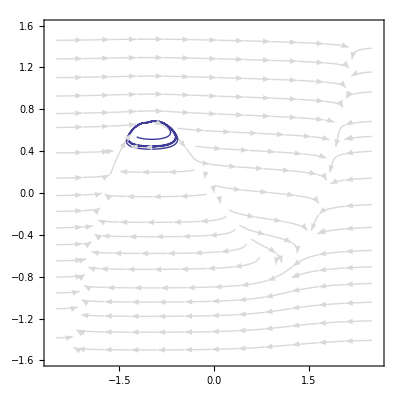

```mathematica
ϵ=.1;
r=.062;
w=1/4;
solution1 =NDSolve[{
x1'[t]==ff1[x1[t],x2[t],λ[t]],
x2'[t]==ff2[x1[t],x2[t],λ[t]],
λ'[t]==ffλ[t],
x1[0]==-1.031977,
x2[0]==0.676699,
λ[0]==0},{x1,x2,λ},{t,0,3000},MaxSteps->300000];
f=ParametricPlot[Evaluate[{x1[t],x2[t]+λ[t]}/.solution1],{t,0,30},PlotRange->{{-2.5,2.5},{-1.5,1.5}},PlotPoints->1000];
Plot[{{x2[t]}/.solution1},{t,00,100},PlotRange->All,Frame->True]
Show[a,f]
```

### Plot progression of limit cycles as rate value increases

```mathematica
ϵ=.1;
r=.02;
f2λ[w_,t_]:=w r/(2Pi) Sin[w t/(2Pi)];
table1=Table[NDSolve[{
x1'[t]==ff1[x1[t],x2[t],λ[t]],
x2'[t]==ff2[x1[t],x2[t],λ[t]],
λ'[t]==f2λ[k,t],
x1[0]==-1.01,
x2[0]==.65,
λ[0]==0},{x1,x2,λ},{t,0,1500},MaxSteps->300000],{k,1,40,1}];
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x1[t],x2[t]+λ[t]}/.table1[[k]]],{t,1000,1500},PlotRange->{{-2.5,2.5},{-1.5,1.5}},PlotPoints->100],{k,1,40,1}];
```

```mathematica
Manipulate[Plot[{x1[t],5λ[t]}/.table1[[k]],{t,1400,1500},PlotRange->{-2.5,2.5},Frame->True],{k,1,40,1}];
```

### Plot progression of trajectories for: ϵ = .3

```mathematica
ϵ=.3;
r=.20;
table1=Table[NDSolve[{
x1'[t]==ff1[x1[t],x2[t],λ[t]],
x2'[t]==ff2[x1[t],x2[t],λ[t]],
λ'[t]==f2λ[k,t],
x1[0]==-1.01,
x2[0]==.6666,
λ[0]==0},{x1,x2,λ},{t,0,1500},MaxSteps->300000],{k,1,40,1}];
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x1[t],x2[t]+λ[t]}/.table1[[k]]],{t,1000,1100},PlotRange->{{-2.5,2.5},{-1.5,1.5}},PlotPoints->100],{k,1,40,1}];
```

# FitzHugh Nagumo System

```mathematica
fv[v_,h_,s_]:= h - (v^3-v+1)/2 - γ s v;
fh[v_,h_,s_]:= -ϵ(2h + 2.6 v);
fs[v_,h_,s_]:= β 1/2(1 + Sign[v])(1-s) -ϵ δ s;
```

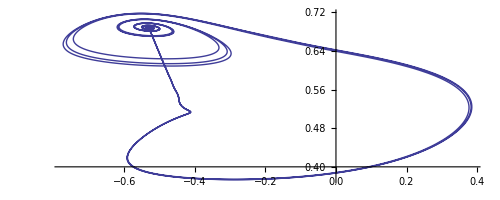

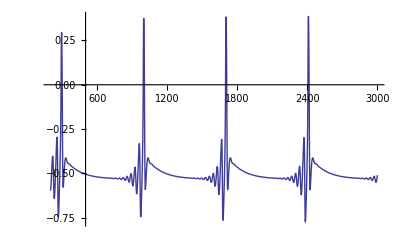

```mathematica
γ=.5;
δ=.565;
ϵ=.015;
β=1;
Clear[v,s,h]
solution1 =NDSolve[{
v'[t]==fv[v[t],h[t],s[t]],
h'[t]==fh[v[t],h[t],s[t]],
s'[t]==fs[v[t],h[t],s[t]],
v[0]==-.5,
h[0]==-6,
s[0]==.6},{v,h,s},{t,0,3000},MaxSteps->200000];ParametricPlot[Evaluate[{v[t],h[t]}/.solution1],{t,800,3000},PlotRange->All,PlotPoints->300]
Plot[Evaluate[{v[t]}/.solution1],{t,200,3000},PlotRange->All]
```

## System With Quadratic Slow Manifold

### Unforced System

```mathematica
ϵ=.1;
```

```mathematica
q1[x1_,x2_,λ_]:=(x2 +λ + (x1^2) ) /ϵ;
q2[x1_,x2_,λ_]:=-x1-1.1;
```

```mathematica
solutionQ =NDSolve[{
x1'[t]==q1[x1[t],x2[t],0],
x2'[t]==q2[x1[t],x2[t],0],
x1[0]==-0.031779913392116284,
x2[0]==0.028326319186810976},{x1,x2},{t,0,10000},MaxSteps->600000];
plot1=ParametricPlot[Evaluate[{x1[t],x2[t]}/.solutionQ],{t,4900,5000},PlotRange->All,PlotPoints->1000,AspectRatio->1];
zz=Plot[-x^2,{x,-.04,.01}];
Plot[{{x1[t]}/.solutionQ},{t,400,500},PlotRange->All,Frame->True];
Show[zz,plot1,PlotRange->All,AspectRatio->1]
```

### Forced System

```mathematica
f1[x1_,x2_,λ_]:=(x2 +λ + (x1^2) ) /ϵ;
f2[x1_,x2_,λ_]:=-x1-.01;
fλ[w_,t_]:= 2Pi w r Sin[2Pi w t];
```

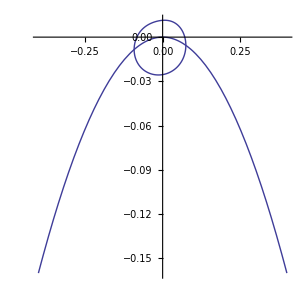

```mathematica
ϵ=.1;
r=.02;
k=.3919135;
k=1/3.0;

solution2 =NDSolve[{
x1'[t]==f1[x1[t],x2[t],λ[t]],
x2'[t]==f2[x1[t],x2[t],λ[t]],
λ'[t]==fλ[k,t],
x1[0]==-0.031779913392116284,
x2[0]==0.028326319186810976,
λ[0]==0},{x1,x2,λ},{t,0,2000},MaxSteps->600000];
plot1=ParametricPlot[Evaluate[{x1[t],x2[t]+λ[t]}/.solution2],{t,1000,1000+1/k-.0},PlotRange->{{-.4,.4},{-.04,.0}},PlotPoints->1000,AspectRatio->1];
zz=Plot[-x^2,{x,-.4,.4}];
Plot[{{x1[t]}/.solution2},{t,400,500},PlotRange->All,Frame->True];
Show[zz,plot1,PlotRange->All,AspectRatio->1]
```

```mathematica
tab=Table[NDSolve[{
x1'[t]==f1[x1[t],x2[t],λ[t]],
x2'[t]==f2[x1[t],x2[t],λ[t]],
λ'[t]==fλ[k,t],
x1[0]==0,
x2[0]==0.001,
λ[0]==0},{x1,x2,λ},{t,0,1200},MaxSteps->300000],{k,1,20,1}];
```

```mathematica
Manipulate[Show[zz,ParametricPlot[Evaluate[{x1[t],x2[t]+λ[t]}/.tab[[k]]],{t,1000,1100},PlotPoints->100],PlotRange->{{-.2,.2},{-.15,.1}}],{k,1,20,1}];
```

## Variational Equations

```mathematica
Clear[M]
```

```mathematica
M[t_]:=Evaluate[{{dxdx0[t],dxdz0[t]},{dzdx0[t],dzdz0[t]}}/.VariationalSolution][[1]]
```

```mathematica
EigenValuesM[t_]:=Eigenvalues[M[t]]
```

```mathematica
EigenValuesM[t_,k_]:=Eigenvalues[M[t].Inverse[M[t-k/ω]]]
```

### Parameters

```mathematica
ϵ=.1;
ω = .33;
r=.02;
α = .01;
```

```mathematica
ϵ=.1;
ω = .34;
r=.02;
α = .01;
VariationalSolution =NDSolve[{
x'[t]==1/ϵ(z[t] + x[t]^2),
z'[t]==-x[t] - α + (2Pi) ω r Sin[2Pi ω t],
dxdx0'[t]==1/ϵ dzdx0[t] + 2/ϵ x[t] dxdx0[t],
dxdz0'[t]== 1/ϵ dzdz0[t] + 2/ϵ x[t] dxdz0[t],
dzdx0'[t]==-dxdx0[t],
dzdz0'[t]==-dxdz0[t],
x[0]==-0.031404053595265005,
z[0]==0.028092221731502894,
dxdx0[0]==1,
dxdz0[0]==0,
dzdx0[0]==0,
dzdz0[0]==1
},{x,z,dxdx0,dxdz0,dzdx0,dzdz0},{t,0,2000},MaxSteps->400000]
M[100]
EigenValuesM[100,1]
Map[Norm,EigenValuesM[100,1]]
```

{{x→InterpolatingFunction[{{0.,2000.}},<>],z→InterpolatingFunction[{{0.,2000.}},<>],dxdx0→InterpolatingFunction[{{0.,2000.}},<>],dxdz0→InterpolatingFunction[{{0.,2000.}},<>],dzdx0→InterpolatingFunction[{{0.,2000.}},<>],dzdz0→InterpolatingFunction[{{0.,2000.}},<>]}}

{{0.000040495,0.0000421217},{-0.0000185525,0.0000510607}}

{-0.704961+0.241512 ⅈ,-0.704961-0.241512 ⅈ}

{0.745184,0.745184}

## Time Scaled Quadratic Slow Manifold

```mathematica
Parameters:
```

```mathematica
ϵ=.1;
ω = .392;
r=.02;
α = .01;
```

```mathematica
TimeScaledSolution =NDSolve[{
x'[t]==1/(ϵ ω)(z[t] + x[t]^2),
z'[t]==1/ω (-x[t] - α) + 2Pi r Sin[2Pi t],
x[0]==-0.031739580566087604,
z[0]==0.028300923959624077},{x,z}, {t,0,15},MaxSteps->400000]
```

{{x→InterpolatingFunction[{{0.,15.}},<>],z→InterpolatingFunction[{{0.,15.}},<>]}}

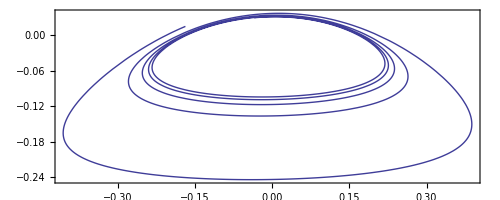

```mathematica
ParametricPlot[{{x[t],z[t]}/.TimeScaledSolution},{t,10,15},PlotRange->All,Frame->True]
```

## Bifurcation Diagram on Quadratic Slow Manifold

```mathematica
G1[x1_,x2_,ϵ_]:=(x2 + x1(x1-1) ) /ϵ;
G2[x1_,x2_]:=-Sum[x1^n,{n,1,5}]+r;
```

```mathematica
p2=Plot[-x(x-1),{x,-10,10},PlotStyle->{Thick,Red}];
```

1.02137

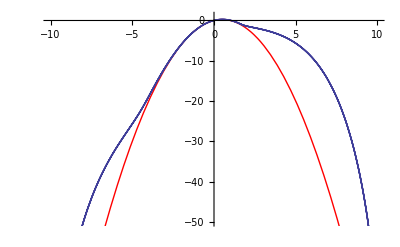

```mathematica
ϵ=.010;
s=.51445821122230001;
r=Sum[s^n,{n,1,5}]
S =NDSolve[{
x1'[t]==G1[x1[t],x2[t], ϵ],
x2'[t]==G2[x1[t],x2[t]],
x1[0]==0,
x2[0]==0},{x1,x2},{t,0,100},MaxSteps->3000000,MaxStepSize->.001];
p3=ParametricPlot[{x1[t],x2[t]}/.S,{t,20,30},PlotPoints->10000];
Show[p2,p3,PlotRange->{{-10,10},{-50,1}}]
```

```mathematica
OOO[t_]=x2[t]/.S[[1]][[2]]
```

InterpolatingFunction[{{0.,100.}},<>][t]

```mathematica
x1[t]/.S[[1]][[1]]
```

InterpolatingFunction[{{0.,100.}},<>][t]

```mathematica
NMaximize[{x1[t]/.S[[1]][[1]],96≤t≤100},t,Method->"SimulatedAnnealing"]
```

{10.1355,{t→96.0674}}

```mathematica
fun[s0_, ϵ0_]:=Module[{ss=s0, ϵ=ϵ0},
r=Sum[ss^n,{n,1,5}];
S =NDSolve[{
x1'[t]==G1[x1[t],x2[t],ϵ],
x2'[t]==G2[x1[t],x2[t]],
x1[0]==0,
x2[0]==0},{x1,x2},{t,0,55},MaxSteps->200000,MaxStepSize->.0005];
OOO[t_]=x1[t]/.S[[1]][[1]];
NMaximize[{OOO[t],25≤t≤55},t,Method->"SimulatedAnnealing"][[1]]
]
```

```mathematica
uuu1= Table[fun[s,0.02],{s,.49,.54, .0001}];
```

```mathematica
uuu2 = Table[fun[s, 0.015],{s,.49,.54, .0001}];
```

```mathematica
uuu3 = Table[fun[s, 0.01],{s,.49,.54, .0001}];
```

```mathematica
vvv=Table[Sum[s^n,{n,1,5}],{s,.49,.54, .0001}];
```

```mathematica
www1=Table[{vvv[[s]],Max[uuu1[[1;;s]]]},{s,1,500}];
www2=Table[{vvv[[s]],Max[uuu2[[1;;s]]]},{s,1,500}];
www3=Table[{vvv[[s]],Max[uuu3[[1;;s]]]},{s,1,500}];
```

```mathematica
www1[[1;;20]]
```

{{0.933645,0.49},{0.93399,0.490101},{0.934337,0.490201},{0.934683,0.490301},{0.935029,0.490401},{0.935375,0.490501},{0.935722,0.490601},{0.936068,0.490701},{0.936415,0.490801},{0.936762,0.490901},{0.937109,0.491001},{0.937456,0.491101},{0.937803,0.491201},{0.93815,0.491301},{0.938497,0.491401},{0.938845,0.491502},{0.939192,0.491602},{0.93954,0.491702},{0.939887,0.491802},{0.940235,0.491903}}

```mathematica
yo=ListPlot[{www3,www2,www1},Joined->True,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"r","Max "Subscript[x,1]},LabelStyle->Directive[14]]
```

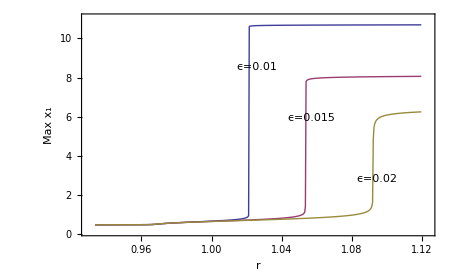

## Bifurcation Diagram on VDP Slow Manifold

```mathematica
G1[x1_,x2_,ϵ_]:=(x2 + x1-x1^3/3) /ϵ;
G2[x1_,x2_]:=-x1-1.01+r;
```

```mathematica
p2=Plot[-x+x^3/3,{x,-10,10},PlotStyle->{Thick,Red}];
```

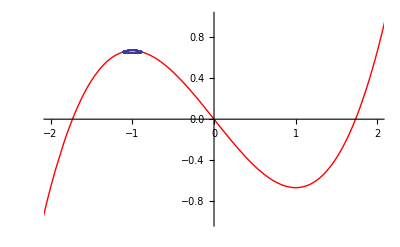

```mathematica
ϵ=.01;
r=.011;
S =NDSolve[{
x1'[t]==G1[x1[t],x2[t], ϵ],
x2'[t]==G2[x1[t],x2[t]],
x1[0]==0,
x2[0]==0},{x1,x2},{t,0,100},MaxSteps->3000000,MaxStepSize->.001];
p3=ParametricPlot[{x1[t],x2[t]}/.S,{t,20,30},PlotPoints->10000];
Show[p2,p3,PlotRange->{{-2,2},{-1,1}}]
```

```mathematica
NMaximize[{x1[t]/.S[[1]][[1]],91≤t≤100},t,Method->"SimulatedAnnealing"]
```

{-0.881901,{t→91.868}}

```mathematica
fun2[s0_, ϵ0_]:=Module[{ss=s0, ϵ=ϵ0},
r=ss;
S =NDSolve[{
x1'[t]==G1[x1[t],x2[t],ϵ],
x2'[t]==G2[x1[t],x2[t]],
x1[0]==0,
x2[0]==0},{x1,x2},{t,0,25},MaxSteps->200000,MaxStepSize->.0005];
OOO[t_]=x1[t]/.S[[1]][[1]];
NMaximize[{OOO[t],10≤t≤25},t,Method->"SimulatedAnnealing"][[1]]
]
```

```mathematica
uuu1= Table[fun2[s,0.02],{s,.012,.016, .00001}]
```

{-0.831735,-0.831455,-0.83039,-0.829543,-0.828599,-0.827642,-0.826608,-0.825723,-0.824723,-0.823706,-0.822677,-0.821611,-0.82056,-0.819474,-0.818379,-0.817234,-0.815915,-0.814948,-0.813802,-0.812573,-0.81136,-0.810078,-0.808836,-0.807526,-0.806074,-0.804797,-0.803354,-0.80191,-0.800426,-0.798863,-0.79729,-0.795665,-0.794026,-0.792241,-0.790462,-0.788575,-0.786608,-0.784544,-0.782395,-0.780126,-0.777732,-0.775192,-0.772483,-0.778664,-0.76644,-0.763032,-0.759287,-0.755105,-0.750364,-0.744865,-0.738275,-0.72997,-0.718536,-0.699308,1.88971,1.90141,1.90454,1.90641,1.90774,1.90878,1.90963,1.91035,1.91097,1.91151,1.912,1.91245,1.91285,1.91322,1.91356,1.91388,1.91418,1.91446,1.91473,1.91498,1.91521,1.91544,1.91566,1.91586,1.91606,1.91625,1.91643,1.9166,1.91677,1.91693,1.91709,1.91724,1.91739,1.91753,1.91766,1.9178,1.91793,1.91805,1.91818,1.9183,1.91841,1.91853,1.91864,1.91875,1.91885,1.91896,1.91906,1.91916,1.91926,1.91935,1.91944,1.91953,1.91962,1.91971,1.9198,1.91988,1.91997,1.92005,1.92013,1.92021,1.92029,1.92036,1.92044,1.92051,1.92058,1.92065,1.92073,1.92079,1.92086,1.92093,1.921,1.92106,1.92113,1.92119,1.92125,1.92132,1.92138,1.92144,1.9215,1.92156,1.92162,1.92167,1.92173,1.92179,1.92184,1.9219,1.92195,1.922,1.92206,1.92211,1.92216,1.92221,1.92226,1.92231,1.92236,1.92241,1.92246,1.92251,1.92256,1.9226,1.92265,1.9227,1.92274,1.92279,1.92283,1.92288,1.92292,1.92297,1.92301,1.92305,1.92309,1.92314,1.92318,1.92322,1.92326,1.9233,1.92334,1.92338,1.92342,1.92346,1.9235,1.92354,1.92358,1.92362,1.92365,1.92369,1.92373,1.92377,1.9238,1.92384,1.92388,1.92391,1.92395,1.92398,1.92402,1.92405,1.92409,1.92412,1.92416,1.92419,1.92422,1.92426,1.92429,1.92432,1.92435,1.92439,1.92442,1.92445,1.92448,1.92452,1.92455,1.92458,1.92461,1.92464,1.92467,1.9247,1.92473,1.92476,1.92479,1.92482,1.92485,1.92488,1.92491,1.92494,1.92497,1.925,1.92502,1.92505,1.92508,1.92511,1.92514,1.92517,1.92519,1.92522,1.92525,1.92527,1.9253,1.92533,1.92536,1.92538,1.92541,1.92543,1.92546,1.92549,1.92551,1.92554,1.92556,1.92559,1.92561,1.92564,1.92567,1.92569,1.92571,1.92574,1.92576,1.92579,1.92581,1.92584,1.92586,1.92589,1.92591,1.92593,1.92596,1.92598,1.926,1.92603,1.92605,1.92607,1.9261,1.92612,1.92614,1.92617,1.92619,1.92621,1.92623,1.92625,1.92628,1.9263,1.92632,1.92634,1.92637,1.92639,1.92641,1.92643,1.92645,1.92647,1.92649,1.92652,1.92654,1.9265,1.92635,1.92609,1.92575,1.92532,1.92482,1.92427,1.92366,1.92301,1.92232,1.92159,1.92084,1.92006,1.91925,1.91843,1.91759,1.91674,1.91587,1.915,1.91411,1.91321,1.91231,1.91141,1.91049,1.90958,1.90866,1.90773,1.90681,1.90588,1.90495,1.90402,1.90309,1.90216,1.90123,1.9003,1.89936,1.89843,1.8975,1.89657,1.89564,1.8947,1.89377,1.89284,1.89192,1.89099,1.89006,1.88913,1.88821,1.88728,1.88636,1.88544,1.88452,1.8836,1.88268,1.88176,1.88084,1.87992,1.87901,1.87809,1.87718,1.87627,1.87536,1.87445,1.87354,1.87263,1.87172,1.87082,1.86991,1.86901,1.86811,1.8672,1.8663,1.8654,1.91532,1.92033,1.92379,1.92603,1.92734,1.92792,1.928,1.92801,1.92803,1.92804,1.92806,1.92808,1.92809,1.92811,1.92812,1.92814,1.92815,1.92817,1.92818,1.9282,1.92822,1.92823,1.92825,1.92826,1.92828,1.92829,1.92831,1.92832,1.92834,1.92835,1.92837,1.92838,1.9284,1.92841,1.92843,1.92844,1.92845,1.92847,1.92848,1.9285,1.92851,1.92853,1.92854,1.92856,1.92857}

```mathematica
uuu2 = Table[fun2[s, 0.03],{s,.012,.016, .00001}]
```

{-0.851284,-0.849916,-0.848662,-0.847523,-0.846497,-0.845583,-0.84478,-0.844086,-0.843499,-0.843019,-0.84259,-0.842159,-0.841726,-0.841292,-0.840856,-0.840418,-0.839978,-0.839536,-0.839092,-0.838647,-0.838199,-0.83775,-0.837298,-0.836845,-0.836389,-0.835932,-0.835472,-0.835011,-0.834547,-0.834082,-0.833614,-0.833144,-0.836053,-0.83552,-0.834985,-0.834448,-0.8329,-0.832383,-0.831865,-0.831344,-0.830821,-0.830296,-0.829769,-0.829239,-0.828708,-0.828173,-0.827637,-0.827098,-0.826557,-0.82674,-0.823773,-0.823255,-0.824013,-0.824528,-0.823952,-0.821154,-0.822138,-0.820086,-0.819548,-0.819007,-0.819866,-0.819001,-0.818713,-0.818132,-0.816256,-0.815696,-0.815727,-0.815149,-0.814568,-0.813984,-0.813396,-0.812805,-0.81221,-0.811612,-0.811673,-0.81105,-0.809795,-0.809182,-0.808565,-0.807944,-0.807993,-0.806258,-0.806587,-0.805934,-0.804376,-0.80374,-0.80409,-0.803414,-0.802735,-0.801723,-0.801048,-0.800368,-0.799158,-0.798805,-0.798566,-0.797856,-0.797093,-0.796376,-0.795653,-0.794925,-0.794191,-0.793451,-0.792735,-0.791982,-0.791224,-0.789954,-0.789202,-0.788444,-0.787679,-0.786907,-0.786127,-0.78562,-0.78472,-0.78391,-0.783275,-0.78244,-0.781587,-0.780737,-0.779883,-0.779014,-0.778136,-0.777249,-0.776351,-0.775419,-0.774503,-0.773576,-0.772638,-0.771622,-0.770746,-0.76977,-0.768632,-0.767781,-0.766704,-0.765679,-0.764688,-0.763629,-0.762554,-0.761447,-0.76034,-0.759214,-0.75807,-0.756905,-0.755727,-0.75452,-0.75329,-0.752037,-0.750759,-0.749454,-0.748122,-0.746728,-0.745367,-0.743947,-0.742463,-0.778662,-0.73944,-0.737868,-0.736267,-0.734561,-0.732849,-0.731083,-0.729258,-0.72737,-0.725412,-0.723379,-0.721264,-0.719069,-0.716754,-0.714346,-0.711806,-0.709128,-0.706292,-0.703276,-0.700052,-0.696584,-0.692833,-0.688733,-0.684211,-0.679151,-0.673395,-0.666693,-0.658629,-0.648426,-0.634333,-0.610671,1.82295,1.84833,1.85398,1.8573,1.85964,1.86146,1.86293,1.86418,1.86525,1.8662,1.86704,1.8678,1.86849,1.86913,1.86972,1.87027,1.87078,1.87126,1.87171,1.87214,1.87254,1.87293,1.87329,1.87364,1.87398,1.8743,1.8746,1.8749,1.87518,1.87546,1.87572,1.87598,1.87623,1.87647,1.8767,1.87693,1.87715,1.87736,1.87757,1.87777,1.87797,1.87816,1.87835,1.87853,1.87871,1.87888,1.87905,1.87922,1.87938,1.87954,1.8797,1.87985,1.88,1.88015,1.8803,1.88044,1.88058,1.88071,1.88085,1.88098,1.88111,1.88124,1.88137,1.88149,1.88161,1.88173,1.88185,1.88197,1.88208,1.88219,1.8823,1.88241,1.88252,1.88263,1.88273,1.88284,1.88294,1.88304,1.88314,1.88324,1.88334,1.88343,1.88353,1.88362,1.88371,1.8838,1.88389,1.88398,1.88407,1.88416,1.88425,1.88433,1.88442,1.8845,1.88458,1.88466,1.88474,1.88482,1.8849,1.88498,1.88506,1.88514,1.88521,1.88529,1.88536,1.88544,1.88551,1.88558,1.88565,1.88573,1.8858,1.88587,1.88594,1.886,1.88607,1.88614,1.88621,1.88627,1.88634,1.8864,1.88647,1.88653,1.8866,1.88666,1.88672,1.88678,1.88685,1.88691,1.88697,1.88703,1.88709,1.88715,1.88721,1.88727,1.88732,1.88738,1.88744,1.88749,1.88755,1.88761,1.88766,1.88772,1.88777,1.88783,1.88788,1.88793,1.88799,1.88804,1.88809,1.88815,1.8882,1.88825,1.8883,1.88835,1.8884,1.88845,1.8885,1.88855,1.8886,1.88865,1.8887,1.88875,1.88879,1.88884,1.88889,1.88894,1.88898,1.88903,1.88908,1.88912,1.88917,1.88922,1.88926,1.88931,1.88935,1.88939,1.88944,1.88948,1.88953,1.88957,1.88961,1.88966,1.8897,1.88974,1.88979,1.88983,1.88987,1.88991,1.88995,1.88999,1.89004,1.89008,1.89012,1.89016,1.8902,1.89024,1.89028,1.89032,1.89036,1.8904,1.89044,1.89047,1.89051,1.89055,1.89059,1.89063,1.89067,1.8907,1.89074,1.89078,1.89082,1.89085,1.89089,1.89093,1.89097,1.891,1.89104}

```mathematica
uuu3 = Table[fun2[s, 0.04],{s,.012,.016, .00001}]
```

{-0.856801,-0.856411,-0.856021,-0.85563,-0.855239,-0.854847,-0.854454,-0.854061,-0.853667,-0.846598,-0.846263,-0.845928,-0.851645,-0.851254,-0.850863,-0.850471,-0.850078,-0.849685,-0.845147,-0.844794,-0.84444,-0.844085,-0.84373,-0.841846,-0.841501,-0.841154,-0.838866,-0.841941,-0.841581,-0.84122,-0.840858,-0.840495,-0.843293,-0.842896,-0.842498,-0.842099,-0.838669,-0.838301,-0.837933,-0.837563,-0.837193,-0.836822,-0.83645,-0.836077,-0.835703,-0.835329,-0.834953,-0.834577,-0.8342,-0.833821,-0.833442,-0.833062,-0.832682,-0.834798,-0.834921,-0.834499,-0.834076,-0.833653,-0.833229,-0.832804,-0.832378,-0.832109,-0.831679,-0.831249,-0.83067,-0.830241,-0.829811,-0.829381,-0.82895,-0.828518,-0.828086,-0.827652,-0.827219,-0.824467,-0.824065,-0.822703,-0.822309,-0.820616,-0.823123,-0.822707,-0.822291,-0.821222,-0.819924,-0.821036,-0.820615,-0.820194,-0.819771,-0.819348,-0.818923,-0.818497,-0.818071,-0.817643,-0.817214,-0.816784,-0.813932,-0.813528,-0.813123,-0.812716,-0.814618,-0.814181,-0.813743,-0.813304,-0.812864,-0.812423,-0.81198,-0.811537,-0.811092,-0.818628,-0.816805,-0.815075,-0.81344,-0.811899,-0.810451,-0.809095,-0.807833,-0.806662,-0.805582,-0.804592,-0.803691,-0.802879,-0.802154,-0.801515,-0.800961,-0.800491,-0.80006,-0.799628,-0.799194,-0.798758,-0.79832,-0.797881,-0.797441,-0.796998,-0.796554,-0.796108,-0.795661,-0.795212,-0.794761,-0.794308,-0.793854,-0.793397,-0.792939,-0.792479,-0.792017,-0.791554,-0.791088,-0.790621,-0.792207,-0.791704,-0.789206,-0.788731,-0.788254,-0.789141,-0.787293,-0.788137,-0.78794,-0.787909,-0.787096,-0.786575,-0.786052,-0.785526,-0.784999,-0.78447,-0.783082,-0.782566,-0.782048,-0.781527,-0.781004,-0.779812,-0.779295,-0.778775,-0.778253,-0.777729,-0.778387,-0.777835,-0.777281,-0.776724,-0.776165,-0.775604,-0.775039,-0.773437,-0.772888,-0.772337,-0.771782,-0.771225,-0.770665,-0.770589,-0.770014,-0.769435,-0.768853,-0.768269,-0.767681,-0.76709,-0.766496,-0.765898,-0.765297,-0.764693,-0.764085,-0.763474,-0.76286,-0.762541,-0.761911,-0.760644,-0.760022,-0.759397,-0.758768,-0.758135,-0.757497,-0.757161,-0.7568,-0.756133,-0.755462,-0.754788,-0.754057,-0.753425,-0.752499,-0.751815,-0.751126,-0.750433,-0.749734,-0.749031,-0.748514,-0.747793,-0.746684,-0.745965,-0.745241,-0.744511,-0.744113,-0.743359,-0.742599,-0.741833,-0.74077,-0.740002,-0.739228,-0.738448,-0.73766,-0.736865,-0.736251,-0.735434,-0.73461,-0.7338,-0.73296,-0.732111,-0.731254,-0.730389,-0.729527,-0.728643,-0.72775,-0.726839,-0.725928,-0.725007,-0.724076,-0.723134,-0.722188,-0.721222,-0.720149,-0.719261,-0.718261,-0.717248,-0.716145,-0.715184,-0.714132,-0.713065,-0.711983,-0.710879,-0.709772,-0.708642,-0.707495,-0.706328,-0.705144,-0.703942,-0.702719,-0.701474,-0.700206,-0.698917,-0.697604,-0.696258,-0.6949,-0.693507,-0.692086,-0.690632,-0.689145,-0.687632,-0.686078,-0.684487,-0.682856,-0.681182,-0.679464,-0.677696,-0.67588,-0.674007,-0.672076,-0.670082,-0.66802,-0.665884,-0.717441,-0.661366,-0.658968,-0.656593,-0.653842,-0.651098,-0.648216,-0.645168,-0.641938,-0.638502,-0.634828,-0.630875,-0.626593,-0.621917,-0.616759,-0.610997,-0.604454,-0.596864,-0.587789,-0.576442,-0.561149,-0.537157,-0.471505,1.78565,1.79687,1.80276,1.80674,1.80975,1.81215,1.81416,1.81588,1.81739,1.81872,1.81992,1.82101,1.822,1.82292,1.82377,1.82457,1.82531,1.82601,1.82666,1.82729,1.82788,1.82844,1.82898,1.82949,1.82998,1.83045,1.8309,1.83134,1.83175,1.83216,1.83255,1.83292,1.83329,1.83364,1.83399,1.83432,1.83464,1.83496,1.83526,1.83556,1.83585,1.83613,1.83641,1.83668,1.83694,1.8372,1.83745,1.8377,1.83794,1.83818,1.83841,1.83863,1.83886,1.83907,1.83929,1.8395,1.8397,1.8399,1.8401,1.8403,1.84049,1.84068,1.84086,1.84105,1.84123,1.8414,1.84158,1.84175,1.84192,1.84208,1.84225,1.84241,1.84257,1.84272,1.84288,1.84303,1.84318,1.84333,1.84348,1.84362,1.84377,1.84391,1.84405,1.84419}

```mathematica
vvv=Table[Sum[s^n,{n,1,5}],{s,.012,.016, .00001}];
```

```mathematica
www1=Table[{vvv[[s]],Max[uuu1[[1;;s]]]},{s,1,400}];
www2=Table[{vvv[[s]],Max[uuu2[[1;;s]]]},{s,1,400}];
www3=Table[{vvv[[s]],Max[uuu3[[1;;s]]]},{s,1,400}];
```

```mathematica
www1[[1;;20]]
```

{{0.933645,0.49},{0.93399,0.490101},{0.934337,0.490201},{0.934683,0.490301},{0.935029,0.490401},{0.935375,0.490501},{0.935722,0.490601},{0.936068,0.490701},{0.936415,0.490801},{0.936762,0.490901},{0.937109,0.491001},{0.937456,0.491101},{0.937803,0.491201},{0.93815,0.491301},{0.938497,0.491401},{0.938845,0.491502},{0.939192,0.491602},{0.93954,0.491702},{0.939887,0.491802},{0.940235,0.491903}}

```mathematica
yo2=ListPlot[{www1,www2,www3},Joined->True,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"r","Max "Subscript[x,1],"van der Pol System"},LabelStyle->Directive[16]]
```